/Users/fuli/Desktop/fortran_test/test

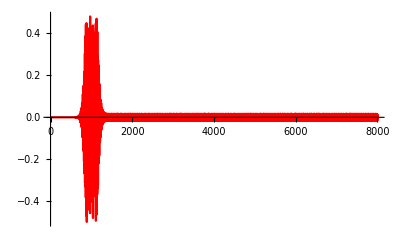

```mathematica
SetDirectory[NotebookDirectory[]]
tend = 8000.0;
t0= 1000.0;
tau = 100.0;
(*s=NDSolve[{x'[t]==-ⅈ*0.05*y[t] *Cos[t],y'[t]==-ⅈ*y[t]-ⅈ*0.05*x[t] *Cos[t],x[0]=={1,0},y[0]=={0,0}},{x,y},{t,tend}];*)
s=NDSolve[{x'[t]==-ⅈ*0.05*y[t]*Exp[-(t-t0)^2/(2*(tau)^2)] *Cos[t],y'[t]==-ⅈ*y[t]-ⅈ*0.05*x[t]*Exp[-(t-t0)^2/(2*(tau)^2)] *Cos[t],x[0]=={1 , 0 } ,y[0]=={0,0 }},{x,y},{t,tend}];
(*p7 = Plot[Evaluate[(Abs[x[t]]^2+Abs[y[t]]^2)/.s],{t,0,tend},PlotRange->All, PlotStyle->Yellow]
p1 = Plot[Evaluate[Abs[x[t]]^2/.s],{t,0,tend},PlotRange->All, PlotStyle->Purple]
p2 = Plot[Evaluate[Abs[y[t]]^2/.s],{t,0,tend},PlotRange->All, PlotStyle->Red];*)
p3 = Plot[Evaluate[Re[x[t].y[t]]/.s],{t,0,tend},PlotRange->All, PlotStyle->Red]
```

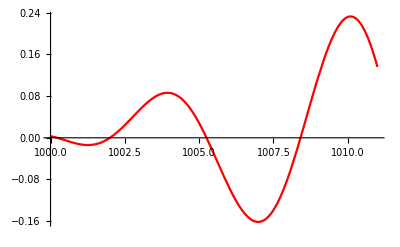

```mathematica
Plot[Evaluate[Re[x[t].y[t]]/.s],{t,1000.0,1011.0},PlotRange->All, PlotStyle->Red]
```

```mathematica
timelist = Range[0,tend,0.1];
fre = 2*Pi*Range[1,Length[timelist]]/tend;
paa=x[timelist]/.s ;
pbb=y[timelist]/.s ;
paa = paa[[1, All, 1]];
pbb = pbb[[1, All, 1]];
pabM =Re[ paa*pbb];
(*ListLinePlot[pabM]*)
ff = Length[timelist]^(1/2)*Fourier[pabM];
```

```mathematica
pabplotF = ListPlot[Thread[{fre, Abs[ff]}],PlotMarkers->"*", PlotRange->{{0.9,1.1},{0,1000}}]
```

-Graphics-